```mathematica
SetDirectory ["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/FREN/order3/PERF/1_fel_fqh/output_0.0001GPa"];
filesPERF={"volume_expansion","volume_expansion_relative","heat_capacity_isobaric","bulk_modulus_isothermal","enthalpy","entropy"};
dataPERF= Table[ReadList[filesPERF[[i]],Table[Number,{i,1,2}]],{i,1,Length[filesPERF]}];
```

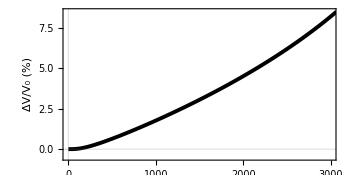

```mathematica
plotStyleVol={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{True,{{0,1000,2000,3000},{}}},PlotStyle->{Black,Thickness[0.008]},FrameLabel->{Style["",16,Black],Style["ΔV/V_0 (%)",16,Black]},FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->350,PlotRange->{{0,3000},{-0.5,8.5}}};
p1=ListLinePlot[dataPERF[[2]],plotStyleVol]
```

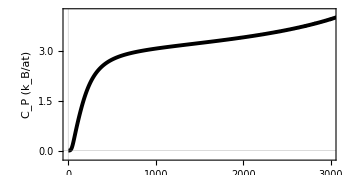

```mathematica
plotStyleHeat={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{True,{{0,1000,2000,3000},{}}},PlotStyle->{Black,Thickness[0.008]},FrameLabel->{Style["",16,Opacity[0]],Style["C_P (k_B/at)",16,Black]},FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->350,PlotRange->{{0,3000},{-0.2,4.2}}};
p2=ListLinePlot[dataPERF[[3]],plotStyleHeat]
```

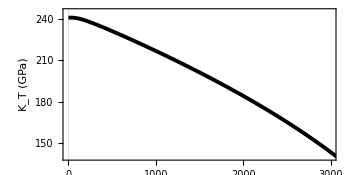

```mathematica
plotStyleBulk={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{True,{{0,1000,2000,3000},{}}},PlotStyle->{Black,Thickness[0.008]},FrameLabel->{Style["",16,Black],Style["K_T (GPa)",16,Black]},FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->350,PlotRange->{{0,3000},{140,245}}};
p3=ListLinePlot[dataPERF[[4]],plotStyleBulk]
```

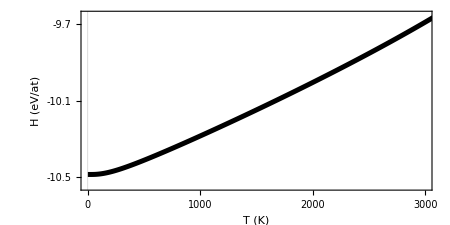

```mathematica
plotStyleEnthalpy={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{{{-10.5,-10.3,-10.1,-9.9,-9.7,-9.5},{}},{{0,1000,2000,3000},{}}},PlotStyle->{Black,Thickness[0.008]},FrameLabel->{Style["T (K)",16,Black],Style["H (eV/at)",16,Black]},FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->450,PlotRange->{{0,3000},{-10.55,-9.65}}};
p4=ListLinePlot[Transpose@{Transpose[dataPERF[[5]]][[1]],Transpose[dataPERF[[5]]][[2]]*0.001},Evaluate@plotStyleEnthalpy]
```

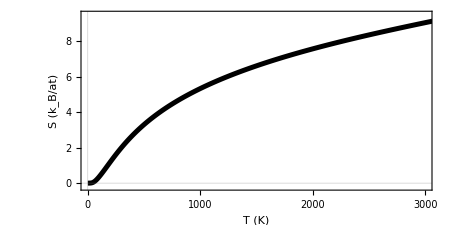

```mathematica
plotStyleEntropy={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",PlotStyle->{Black,Thickness[0.008]},PlotRange->{{0,3000},{-0.2,9.5}},FrameStyle->Directive[18,Black,Thickness[0.01]],FrameLabel->{Style["T (K)",16,Black],Style["S (k_B/at)",16,Black]},FrameTicks->{{{0,2,4,6,8},{}},{{0,1000,2000,3000},{}}},ImageSize->450};
ListLinePlot[dataPERF[[6]],plotStyleEntropy]
```

```mathematica
ListPlot@Transpose@{Transpose[dataFREN[[1]]][[1]],Transpose[dataFREN[[1]]][[2]]}
```

Part::partd: Part specification dataFREN⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 2 of Transpose[dataFREN⟦1⟧] does not exist.

Transpose::nmtx: The first two levels of {dataFREN⟦1⟧,Transpose[dataFREN⟦1⟧]⟦2⟧} cannot be transposed.

ListPlot::lpn: Transpose[{dataFREN⟦1⟧,Transpose[dataFREN⟦1⟧]⟦2⟧}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{dataFREN⟦1⟧,Transpose[dataFREN⟦1⟧]⟦2⟧}]]

```mathematica
names={"B_2","B_3","U_2","U_3","U_4"};
SetDirectory ["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/FREN/order3"];
filesFREN={"volume_expansion.2_fqh_fel_sizeFINITE.all","volume_expansion_relative.2_fqh_fel_sizeFINITE.all","heat_capacity_isobaric.2_fqh_fel_sizeFINITE.all","bulk_modulus_isothermal.2_fqh_fel_sizeFINITE.all","enthalpy.2_fqh_fel_sizeFINITE.all","entropy.2_fqh_fel_sizeFINITE.all"};
dataFREN= Table[ReadList[filesFREN[[i]],Table[Number,{i,1,6}]],{i,1,Length[filesFREN]}];
```

```mathematica
{Directive[{Thickness[0.014],Dashing[Tiny]}],Directive[{Thickness[0.014],Dashing[Small]}],Directive[{Thickness[0.014],Dashing[Medium]}]}
Table[Directive[{Thickness[0.014],Dashing[0.02*i]}],{i,1,3}]
{Directive[{Thickness[0.014],Dashing[Small]}],Directive[{Thickness[0.014],Dashing[Medium]}],Directive[{Thickness[0.014],Dashing[Large]}]}
```

{Directive[{Thickness[0.014],Dashing[Tiny]}],Directive[{Thickness[0.014],Dashing[Small]}],Directive[{Thickness[0.014],Dashing[Medium]}]}

{Directive[{Thickness[0.014],Dashing[0.02]}],Directive[{Thickness[0.014],Dashing[0.04]}],Directive[{Thickness[0.014],Dashing[0.06]}]}

{Directive[{Thickness[0.014],Dashing[Small]}],Directive[{Thickness[0.014],Dashing[Medium]}],Directive[{Thickness[0.014],Dashing[Large]}]}

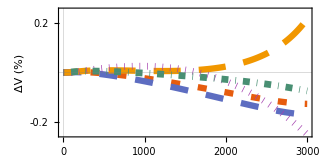

```mathematica
g[arg_]:=Style[arg,18]
styles=Flatten@Join[{Table[Directive[{Thickness[0.014],Dashing[{0.02*i,0.04}]}],{i,1,3}],Directive[{Thickness[0.015],Dotted}],Directive[{Thickness[0.015],DotDashed}]}];


plotStyleVolf={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{{{-0.2,0.0,0.2,0.4,0.6},{}},{{0,1000,2000,3000},{}}},PlotStyle->styles,FrameLabel->{Style["T (K)",16,Black],Style["ΔV (%)",16,Black]},FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->325,PlotRange->{{0,3000},{-0.25,0.25}}};
oldq0=ListLinePlot[Table[Transpose@{Transpose[dataFREN[[1]]][[1]],Transpose[dataFREN[[2]]][[1+i]]},{i,1,5}],plotStyleVolf]
```

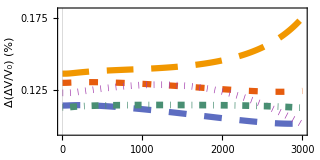

```mathematica
plotStyleVolf={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{{{0,0.1,0.125,0.15,0.175},{}},{{0,1000,2000,3000},{}}},PlotStyle->styles,FrameLabel->{Style["T (K)",16,Black],Style["Δ(ΔV/V_0) (%)",16,Black]},FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->320,PlotRange->{{0,3000},{0.095,0.18}}};
q0=ListLinePlot[Table[Transpose@{Transpose[dataFREN[[1]]][[1]],Transpose[dataFREN[[1]]][[1+i]]},{i,1,5}],plotStyleVolf]
```

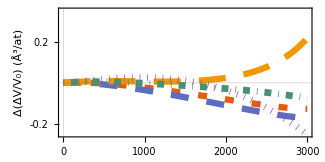

```mathematica
plotStyleVolf={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{{{-0.2,0.0,0.2,0.4,0.6},{}},{{0,1000,2000,3000},{}}},PlotStyle->styles,FrameLabel->{Style["T (K)",16,Black],Style["Δ(ΔV/V_0) (Å^3/at)",16,Black]},FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->325,PlotRange->{{0,3000},{-0.25,0.35}}};
q1=ListLinePlot[Table[Transpose@{Transpose[dataFREN[[2]]][[1]],Transpose[dataFREN[[2]]][[1+i]]},{i,1,5}],plotStyleVolf]
```

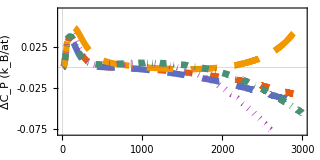

```mathematica
plotStyleHeatf={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",PlotStyle->styles,FrameTicks->{{{-0.075,-0.05,-0.025,0.00,0.025,0.05},{}},{{0,1000,2000,3000},{}}},FrameLabel->{Style["T (K)",16,Black],Style["ΔC_P (k_B/at)",16,Black]},FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->320,PlotRange->{{0,3000},{-0.08,0.07}}};
q2=ListLinePlot[Table[MovingAverage[Transpose@{Transpose[dataFREN[[3]]][[1]],Transpose[dataFREN[[3]]][[1+i]]},13],{i,1,5}],plotStyleHeatf]
```

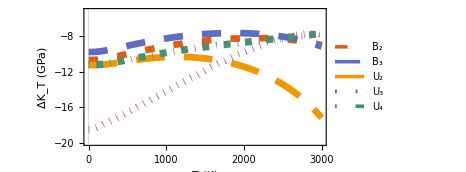

```mathematica
plotStyleBulk={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{{Automatic,{}},{{0,1000,2000,3000},{}}},PlotStyle->styles,FrameLabel->{Style["T (K)",16,Black],Style["ΔK_T (GPa) ",16,Black]},FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->345
,PlotRange->{{0,3000},{-20,-5.20}},PlotLegends->Table[g[names[[i]]],{i,1,Length@names}]};
q3=ListLinePlot[Table[Transpose@{Transpose[dataFREN[[4]]][[1]],Transpose[dataFREN[[4]]][[1+i]]},{i,1,5}],plotStyleBulk]
```

```mathematica
relativeThermodynamics=GraphicsGrid[{{p1,p2,p3},{q0,q2,q3}},ImageSize->1200,Spacings->-27]
```

-Graphics-

```mathematica
Export["/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/thermodynamics.pdf",relativeThermodynamics];
```

```mathematica
GraphicsGrid[{{q0,q2,q3}},ImageSize->1200]
```

-Graphics-

-Graphics-

```mathematica
f[arg_]:=Style[arg,18]
f["B_2"];
names2={"B_2","B_3","U_2","U_3","U_4"};
```

```mathematica
styles2=Flatten@Join[{Table[Directive[{Thickness[0.018],Dashing[{0.02*i,0.04}]}],{i,1,3}],Directive[{Thickness[0.019],Dotted}],Directive[{Thickness[0.019],DotDashed}]}];
```

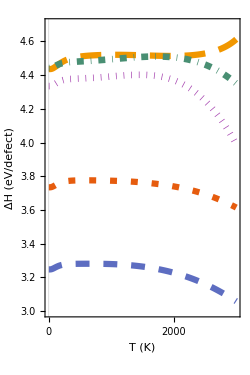

```mathematica
plotStyleEnthalpy={AspectRatio->1.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{True,{{0,1000,2000,3000},{}}},PlotStyle->styles2,FrameLabel->{Style["T (K)",16,Black],Style["ΔH (eV/defect)",16,Black]},FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->{250,250},PlotRange->{{0,3001},{3,4.7}}};
q4=ListLinePlot[Table[Transpose@{Transpose[dataFREN[[5]]][[1]],Transpose[dataFREN[[5]]][[1+i]]*64/1000},{i,1,5}],plotStyleEnthalpy]
```

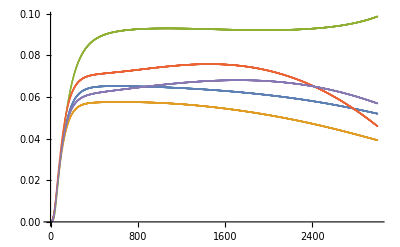

```mathematica
ListPlot[Transpose[dataFREN[[6]][[1;;3000]]][[2;;6]]]
```

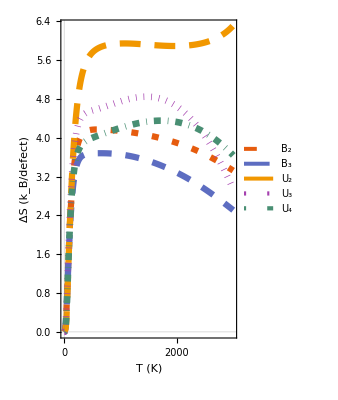

```mathematica
plotStyleEnthalpy={AspectRatio->1.6,Frame->True,PlotTheme->"Scientific",FrameTicks->{True,{{0,1000,2000,3000},{}}},PlotStyle->styles2,FrameLabel->{Style["T (K)",16,Black],Style["ΔS (k_B/defect) ",16,Black]},FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->{250,250},PlotRange->{{0,3001},{-0.00,6.3}},PlotLegends->Placed[LineLegend[Table[f[names2[[i]]],{i,1,Length@names}],LegendMarkerSize->{45,2}],{0.33,0.28}]};
q5=ListLinePlot[Table[Transpose@{Transpose[dataFREN[[6]]][[1]],Transpose[dataFREN[[6]]][[1+i]]*64},{i,1,5}],plotStyleEnthalpy]
```

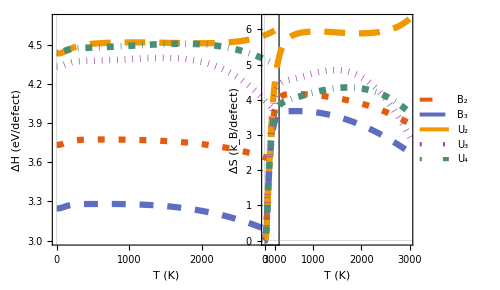

```mathematica
enthalpy=GraphicsGrid[{{q4,q5}},Spacings->-70,ImageSize->500,PlotRangePadding->None]
```

```mathematica
33
```

33

```mathematica
Export["/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/enthalpy.pdf",enthalpy];
```

```mathematica
grid=GraphicsGrid[Transpose@{{p1,p2,p3},{q1,q2,q3}},Spacings->-10];
plot=Show[grid,ImageSize->600]
```

-Graphics-

```mathematica
Export["/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/thermodynamics.eps",plot];
```